# Poroke v Sloveniji Analiza porok v Sloveniji glede na različne dejavnike

## Analiza sklenitve zakonskih zvez po mesecih med letoma 2000 in 2020

Pridobivanje in urejanje podatkov (vse podatke sem pridobila iz Statističnega urada Republike Slovenije).

```mathematica
meseci = Import[NotebookDirectory[]<>"meseci.csv","Table",FieldSeparators->";",HeaderLines->3,CharacterEncoding->"WindowsEastEurope"]//Prepend[#,{"leto","mesec","stevilo"}]&//ResourceFunction["DatasetWithHeaders"]
```

Analizirala bom podatke glede na mesec sklenitve poroke . Najprej bom narisala graf, ki prikazuje skupno število porok v posameznem letu med letoma 2000 in 2020. Videli bomo upad oz. naraščaj porok med leti. Nato bom narisala še stolpični in krožni diagram za lažji prikaz povprečja števila porok za posamezni mesec. Tako bomo videli v katerem mesecu je bilo sklenjenih največ porok.

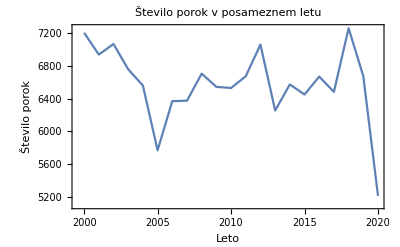

```mathematica
letnice = meseci//Values//Query[All,First]//Normal//Union;

SkupnoPorok[letnica_]:=meseci//Query[Select[#leto==letnica&],Last]//Normal//Total;

leta =Table[{x, SkupnoPorok[x]},{x,letnice}];

leta//Dataset//ListLinePlot[
#,PlotLabel->"Število porok v posameznem letu",FrameLabel->{ "Leto", "Število porok"},Frame-> {{True, False}, {True, False}}]&
```

```mathematica
vsePoroke = meseci//Query[All,Last]//Normal//Total
```

138089

### V katerem mesecu je največ porok?

-Graphics-

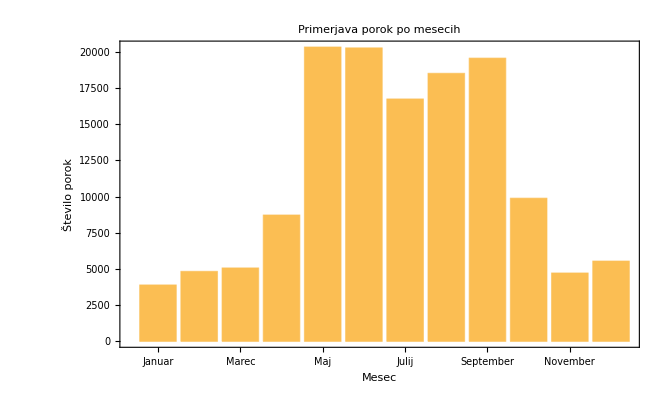

```mathematica
procenti[kaj_,vse_]:=PercentForm[N[kaj/vse]]

kateri = meseci//
Query[GroupBy[{#mesec}&]/*Values,<|"mesec"-> Query[First,"mesec"],  
"skupno" -> Query[Total, "stevilo"]|>]//
Query[All, <|#, "procenti" -> procenti[#skupno,vsePoroke]|>&]

kateri//
PieChart[
# // Query[All, "skupno"], 
ChartLegends-> (# //  Query[All, "mesec"] // Normal),ChartLabels->{# //  Query[All, "procenti"] // Normal}
]&

kateri//
BarChart[
# // Query[All, "skupno"],ChartLabels->{# //  Query[All, "mesec"] // Normal},PlotLabel->"Primerjava porok po mesecih",FrameLabel->{ "Mesec", "Število porok"},Frame-> {{True, False}, {True, False}}
]&
```

## Analiza sklenitve prvih zakonskih zvez po starosti in spolu v letu 2020

Pridobivanje in urejanje podatkov.

```mathematica
prvic = Import[NotebookDirectory[]<> "prvic.csv","Table", FieldSeparators -> ";", HeaderLines -> 3, CharacterEncoding->"WindowsEastEurope"]//Prepend[#,{"starost", "leto", "spol","stevilo"} ]& //ResourceFunction["DatasetWithHeaders"]//
Query[All, <|  #,"stevilo" -> If[#stevilo == "-", 0, #stevilo] |>&]
```

Analizirala bom podatke glede na sklenitev prve zakonske zveze po starosti in spolu v letu 2020. Najprej bom narisala stolpični diagram, ki prikazuje število porok za posamezno starostno skupino. Graf bo skupen za oba spola, saj ju bomo tako lažje primerjali. Videli bomo tudi pri kateri starosti se poroči največ pripradnikov določenega spola.
Nato bom narisala dva grafa za primerjavo števila porok ženina in neveste starih 20-24 med leti 2000 in 2020, da vidimo ali se je število kaj spremenilo. Nato bom za lažjo primerjavo med spoloma oba grafa združila, da vidimo koliko se število porok med spoloma razlikuje.

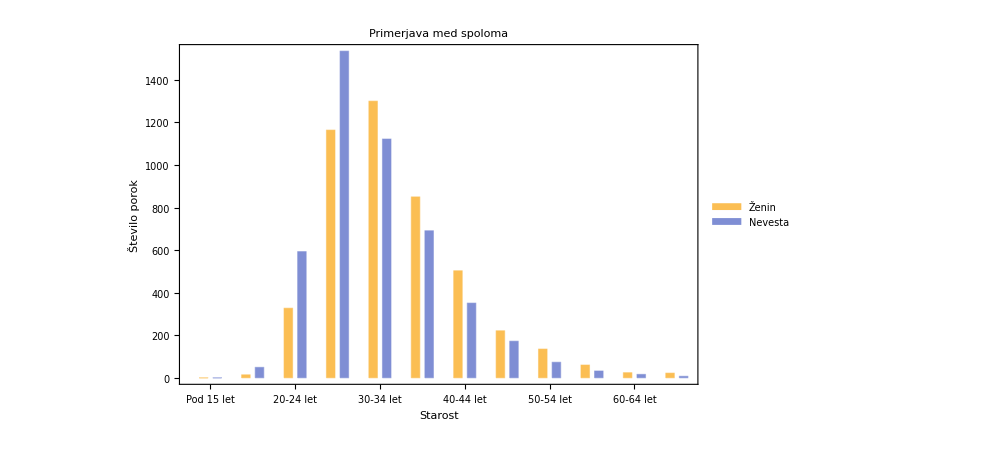

```mathematica
precisceni = prvic//Query[Select[#leto ==2020&],All];

starost = precisceni //Values//Query[All,First]//Normal//DeleteDuplicates;

zenin = precisceni//Query[Select[#spol == "Ženin"&], All] //Values//Query[All,Last]//Normal;

nevesta = precisceni//Query[Select[#spol== "Nevesta"&], All ] //Values//Query[All,Last]//Normal;

pari =Table[{zenin[[i]],nevesta[[i]]},{i, Length[zenin]}];

BarChart[pari, ChartLabels->{starost,{,}},ChartLegends->{"Ženin","Nevesta"},PlotLabel->"Primerjava med spoloma",FrameLabel->{ "Starost", "Število porok"},Frame-> {{True, False}, {True, False}}]
```

```mathematica
ClearAll[zenin,nevesta]
```

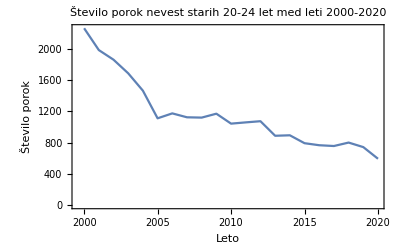

```mathematica
nevesta = prvic //
Query[
Select[#starost == "20-24 let" &&
#spol == "Nevesta"&
]
] // 
Query[SortBy[#leto&]] //
Query[All, <| "leto" -> #leto,
"stevilo" -> #stevilo |>&]//
ListLinePlot[
#, 
PlotLabel->"Število porok nevest starih 20-24 let med leti 2000-2020", 
FrameLabel->{ "Leto", "Število porok"},
Frame-> {{True, False}, {True, False}}
]&
```

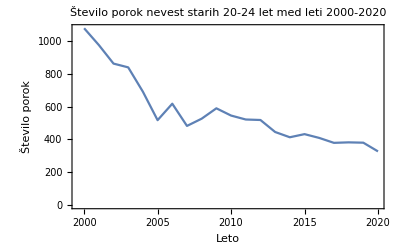

```mathematica
zenin = prvic //
Query[
Select[#starost == "20-24 let" &&
#spol == "Ženin"&
]
] // 
Query[SortBy[#leto&]] //
Query[All, <| "leto" -> #leto,
"stevilo" -> #stevilo |>&]//
ListLinePlot[
#, 
PlotLabel->"Število porok nevest starih 20-24 let med leti 2000-2020", 
FrameLabel->{ "Leto", "Število porok"}, 
Frame-> {{True, False}, {True, False}}
]&
```

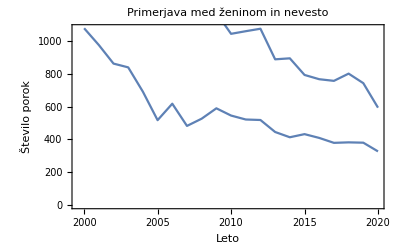

```mathematica
Show[{zenin,nevesta},PlotLabel->"Primerjava med ženinom in nevesto"]
```

## Analiza sklenitve zakonskih zvez po vrstnem redu sklenitve zakonske zveze ženina in neveste med leti 2000 in 2020

Pridobivanje podatkov.

```mathematica
stevilo = Import[NotebookDirectory[]<> "stevilo.csv","Table", FieldSeparators -> ";", HeaderLines -> 3, CharacterEncoding->"WindowsEastEurope"]//Prepend[#,{"ženin", "nevesta", "leto", "stevilo"} ]& //ResourceFunction["DatasetWithHeaders"]//Query[All, <|  #,"stevilo" -> If[#stevilo == "-", 0, #stevilo] |>&]
```

Analizirala bom podatke glede na vrstni red sklenitve zakonske zveze ženina in neveste med leti 2000 in 2020. Narisala bom graf s pomočjo funkcije Manipulate. Videli bomo kako se število porok po vrstnem redu spreminja.

```mathematica
ClearAll[zenin,nevesta]
```

```mathematica
sez1 = stevilo//Values//Query[All,First]//Normal//DeleteDuplicates;
sez2 = stevilo//Query[
GroupBy[{#nevesta} &]/* Values, 
<|  
"nevesta"-> Query[First,"nevesta"]|>
] //Values//Query[All,First]//Normal;
```

```mathematica
Funkcija[zenin_,nevesta_] := stevilo //
Query[
Select[#ženin == zenin &&
#nevesta ==  nevesta&
]
] // 
Query[SortBy[#leto&]] //
Query[All, <| "leto" -> #leto,
"stevilo" -> #stevilo |>&]//
ListLinePlot[
#,  
FrameLabel->{ "Leto", "Število porok"}, 
Frame-> {{True, False}, {True, False}}
]&;

Manipulate[Funkcija[Ženin,Nevesta],{Ženin,sez1},{Nevesta,sez2}]
```